```mathematica
l[n_,p_,k_]:=PDF[BinomialDistribution[n,p],k]
k1=20;
k2=15;
c=3;
MinN=k1+k2-c;
f[p1_,p2_,n_]:=l[n,p1,k1]*l[n-k1,p2,k2-c]*l[k1,p2,c]
un=UniformDistribution[{0,1}];
normP=NormalDistribution[0,.05];
normN=NormalDistribution[0,5];
Clamp[p_]:=Min[Max[p,0],1]
ClampN[n_]:=Max[Round[n],MinN]
step[{p1_,p2_,n_}]:=With[
{
u=RandomVariate[un],
p1p=Clamp[RandomVariate[normP]+p1],
p2p=Clamp[RandomVariate[normP]+p2],
np=ClampN[RandomVariate[normN]+n]
},
If[u≤f[p1p,p2p,np]/f[p1,p2,n],{p1p,p2p,np},{p1,p2,n}]
]
samples=NestList[step,{.23,.17,100},1000000];
{p1M,p2M,nM}=samplesᵀ;
```

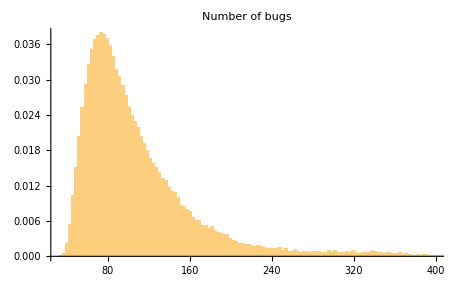

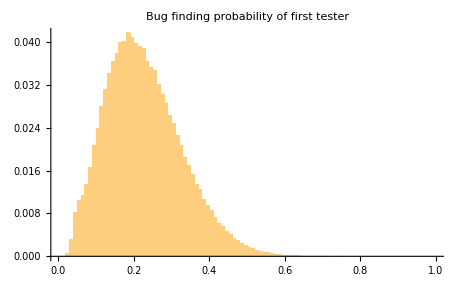

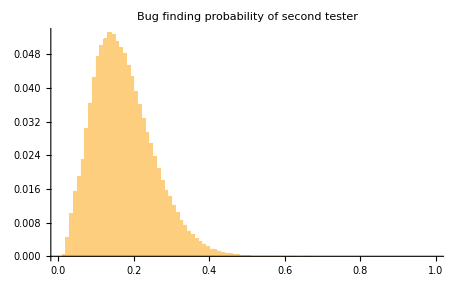

```mathematica
Histogram[nM,{3},"Probability",PlotLabel->"Number of bugs",PlotRange->{{MinN,400},Automatic}]
Histogram[p1M,{.01},"Probability",PlotLabel->"Bug finding probability of first tester",PlotRange->{{0,1},Automatic}]
Histogram[p2M,{.01},"Probability",PlotLabel->"Bug finding probability of second tester",PlotRange->{{0,1},Automatic}]
```

```mathematica
nMClean=DeleteCases[nM,_?#>400&];
Mean[nMClean]//N
Mean[p1M]
Mean[p2M]
```

111.78

0.22649

0.172636